```mathematica
PacletDirectoryLoad["C:/Users/karlc/Documents/MathematicaPackages/KerrGeodesics"]
<<KerrGeodesics`
SetDirectory[NotebookDirectory[]]
```

{C:\Users\karlc\Documents\MathematicaPackages\KerrGeodesics}

C:\Users\karlc\Documents\Stage 4 Research Project\Thesis\Presentation

## Schwarzschild Example plots

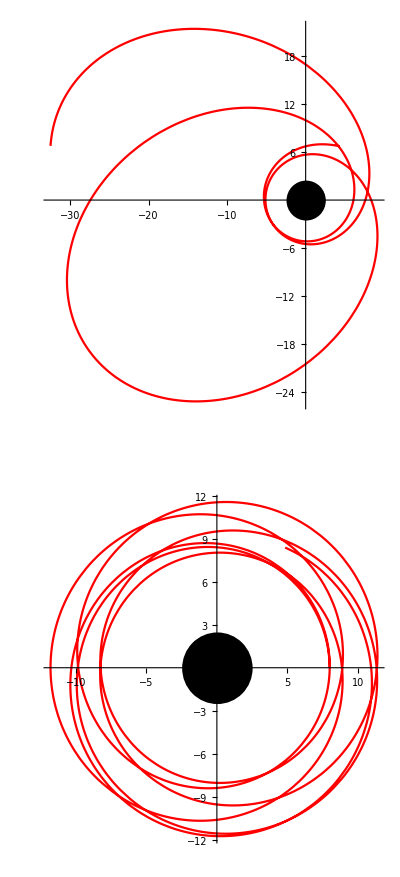

```mathematica
f[M_,r_]:=1-(2 M)/r;
OrbitalSolve[r0_,ϕ0_,E0_,M0_,L0_]:=First@NDSolve[{ϕ'[τ]-L0/r[τ]^2==0,ϕ[0]==ϕ0,3 L0^2-L0^2 r[τ]+r[τ]^2+r[τ]^4 r''[τ]==0,r[0]==r0,r'[0]^2==E0^2-f[M0,r0](1+L0^2/r0^2)},{r,ϕ},{τ,0,1000}];
With[{M0=1,r0=8},
E0=0.976;
L0=3.842;
{RSolELMatch,ASolELMatch}=OrbitalSolve[r0,1,E0,1,L0];
nonEcPlot=Show[ParametricPlot[{RSolELMatch[[2]][τ] Cos[ASolELMatch[[2]][τ]],RSolELMatch[[2]][τ] Sin[ASolELMatch[[2]][τ]]},{τ,0,1000}, PlotStyle->Red, TicksStyle->Directive["Label", 14], AxesStyle->Directive[Black,Thickness[0.006]]],Graphics[Disk[{0,0},2.5]]];
E0=0.956;
L0=3.74;
{RSolELMatch,ASolELMatch}=OrbitalSolve[r0,0,E0,1,L0];
ecPlot=Show[ParametricPlot[{RSolELMatch[[2]][τ] Cos[ASolELMatch[[2]][τ]],RSolELMatch[[2]][τ] Sin[ASolELMatch[[2]][τ]]},{τ,0,1000}, PlotStyle->Red,TicksStyle->Directive["Label", 14], AxesStyle->Directive[Black,Thickness[0.005]]],Graphics[Disk[{0,0},2.5]]];
symmetryexample=GraphicsColumn[{nonEcPlot,ecPlot}]]
```

```mathematica
Export["SchwarzOrbitEcc.pdf",ecPlot]
Export["SchwarzOrbitNonEcc.pdf",nonEcPlot]
```

SchwarzOrbitEcc.pdf

SchwarzOrbitNonEcc.pdf

## Potential Energy Graph

```mathematica
VLr[L_,r_,M_]:=(1-2M/r)(1+L^2/r^2)
```

```mathematica
With[{M=1,L=3.9},rmax=FindRoot[D[VLr[3.9,r/3,1],r]==0,{r,10}];
vmax=VLr[L,r/3,M]/.rmax]
```

0.975642

```mathematica
With[{M=1,L=3.9},rmin=FindRoot[D[VLr[3.9,r/3,1],r]==0,{r,40}];
vmin=VLr[L,r/3,M]/.rmin]
```

0.921025

```mathematica
line1=Line[{{9.788709362260839,0},{9.788709362260839,0.94}}];
line2=Line[{{19.885190428465002,0},{19.885190428465002,0.94}}];
line3=Line[{{70.32610020927416,0},{70.32610020927416,0.94}}];
```

```mathematica
eUnstableTxt=Text[Style["E_Unstable",14],Scaled[{0.42,0.9}],{0,0},Background->White];
eBoundTxt=Text[Style["E_Bound",14],Scaled[{0.42,0.5}],{0,0},Background->White];
eStableTxt=Text[Style["E_Circular",14],Scaled[{0.42,0.31}],{0,0},Background->White];
r1Txt=Text[Style["r_1",14],Scaled[{0.1,0.385}],{0,0},Background->White];
r2Txt=Text[Style["r_2",14],Scaled[{0.22,0.385}],{0,0},Background->White];
r3Txt=Text[Style["r_3",14],Scaled[{0.91,0.385}],{0,0},Background->White];
txt=Graphics[{eUnstableTxt,eBoundTxt,eStableTxt,r1Txt,r2Txt,r3Txt}];
```

```mathematica
(* ticks = {{{9.788709362260839,"r_3"},{19.885190428465002,"r_1"},{70.32610020927416,"r_2"}},{{0.94,"E^2"}}} *)
```

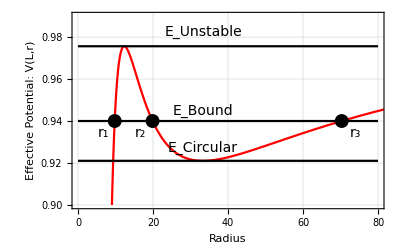

```mathematica
radialPE=Show[{Plot[VLr[3.9,r/3,1],{r,2,200},PlotRange->{{0,80},{0.9,0.99}},PlotStyle->Red,FrameLabel->{"Radius","Effective Potential: V(L,r)"},LabelStyle->Directive[12],Frame->True,GridLines->Automatic],
Plot[{0.94},{r,0,80},PlotStyle->Black],
Plot[{vmax},{r,0,80},PlotStyle->Black],
Plot[{vmin},{r,0,80},PlotStyle->Black],
Graphics[{PointSize[0.025],Black,Point[{9.788709362260839,0.94}]}],
Graphics[{PointSize[0.025],Black,Point[{19.885190428465002,0.94}]}],
Graphics[{PointSize[0.025],Black,Point[{70.32610020927416,0.94}]}]},
txt]
```

```mathematica
Export["RadialPotentialPE.pdf",radialPE]
```

RadialPotentialPE.pdf

## Kerr Example plots

```mathematica
orbit=KerrGeoOrbit[0.9,4.4,0.4,0.8];
{t,r,θ,φ}=orbit["Trajectory"];
kerrExample1=Show[ParametricPlot3D[{r[λ] Sin[θ[λ]] Cos[φ[λ]],r[λ] Sin[θ[λ]] Sin[φ[λ]],r[λ] Cos[θ[λ]]},{λ,0,20},ImageSize->700,Boxed->False,Axes->False,PlotStyle->{Red,Thickness[0.004]},PlotRange->All],Graphics3D[{Black,Sphere[{0,0,0},1+Sqrt[1-0.998^2]]}]]
```

-Graphics3D-

```mathematica
vp=Options[Graphics3D,ViewPoint][[1,2]];
orbit=KerrGeoOrbit[0.99,4.304412839914767,0.7,0.65];
{t,r,θ,φ}=orbit["Trajectory"];
kerrExample2=Show[ParametricPlot3D[{r[λ] Sin[θ[λ]] Cos[φ[λ]],r[λ] Sin[θ[λ]] Sin[φ[λ]],r[λ] Cos[θ[λ]]},{λ,0,90},ImageSize->700,Boxed->False,Axes->False,PlotStyle->{Red,Thickness[0.003]},PlotRange->All,ViewPoint->Dynamic[vp]],Graphics3D[{Black,Sphere[{0,0,0},1+Sqrt[1-0.998^2]]}]]
```

-Graphics3D-

```mathematica
orbit=KerrGeoOrbit[0.9999,1.08195,0.001,0.99];
{t,r,θ,φ}=orbit["Trajectory"];
kerrExample3=Show[ParametricPlot3D[{r[λ] Sin[θ[λ]] Cos[φ[λ]],r[λ] Sin[θ[λ]] Sin[φ[λ]],r[λ] Cos[θ[λ]]},{λ,0,90},ImageSize->700,Boxed->False,Axes->False,PlotStyle->{Red,Thickness[0.002]},PlotRange->All],Graphics3D[{Black,Sphere[{0,0,0},1+Sqrt[1-0.998^2]]}]]
```

-Graphics3D-

```mathematica
Export["kerrExample1.pdf",kerrExample1]
Export["kerrExample2.pdf",kerrExample2]
Export["kerrExample3.pdf",kerrExample3]
```

kerrExample1.pdf

kerrExample2.pdf

kerrExample3.pdf

## r-θ resonance plots

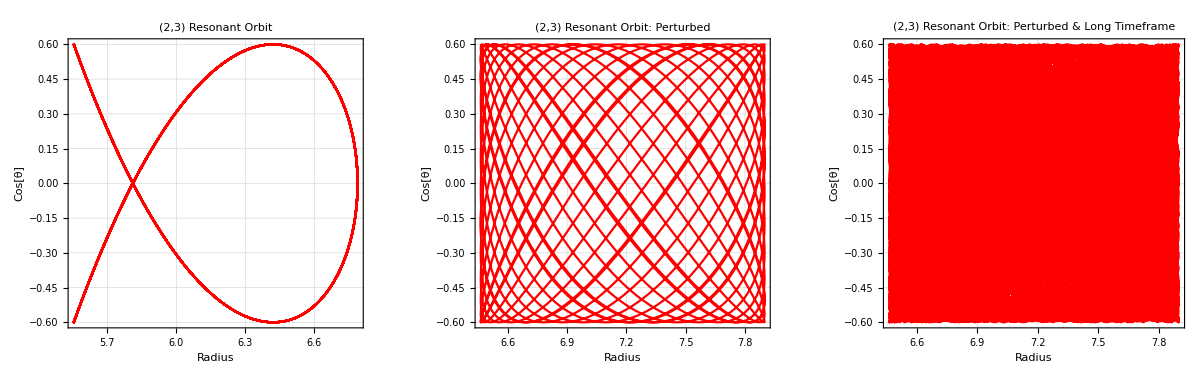

```mathematica
With[{a=0.9,e=0.1,x=0.8,fontmain=14, fontacc=12},
pRes=KerrGeoFindResonance[<|"a"->a,"e"->e,"x"->x|>,{2,3,0}];
orbit=KerrGeoOrbit[a,pRes[[2]],e,x];
{t,r,θ,ϕ}=orbit["Trajectory"];
KerrRTh=ParametricPlot[{r[λ],Cos[θ[λ]]},{λ,0,50},PlotStyle->Red,AspectRatio->1,FrameLabel->{Style["Radius",fontmain],Style["Cos[θ]",fontmain]},FrameTicksStyle->Directive[fontacc],GridLines->Automatic,Frame->True,PlotLabel->Style["(2,3) Resonant Orbit", fontmain]];
orbit=KerrGeoOrbit[a,pRes[[2]]+1,e,x];
{t,r,θ,ϕ}=orbit["Trajectory"];
KerrRThPert=ParametricPlot[{r[λ],Cos[θ[λ]]},{λ,0,50},PlotStyle->Red,AspectRatio->1,FrameLabel->{Style["Radius",fontmain],Style["Cos[θ]",fontmain]},FrameTicksStyle->Directive[fontacc],GridLines->Automatic,Frame->True,PlotLabel->Style["(2,3) Resonant Orbit: Perturbed", fontmain]];
KerrRThPertFull=ParametricPlot[{r[λ],Cos[θ[λ]]},{λ,0,500},PlotStyle->Red,AspectRatio->1,FrameLabel->{Style["Radius",fontmain],Style["Cos[θ]",fontmain]},FrameTicksStyle->Directive[fontacc],GridLines->Automatic,Frame->True,PlotLabel->Style["(2,3) Resonant Orbit: Perturbed & Long Timeframe", fontmain]];]
GraphicsRow[{KerrRTh,KerrRThPert,KerrRThPertFull}]
```

```mathematica
Export["rTheta23Reso.pdf",KerrRTh]
Export["rTheta23ResoPert.pdf",KerrRThPert]
Export["rTheta23ResoPertFull.pdf",KerrRThPertFull]
```

rTheta23Reso.pdf

rTheta23ResoPert.pdf

rTheta23ResoPertFull.pdf